## Neuron model, synaptic plasticity rule and learning of spike timings

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

## Code

### Init

```mathematica
$HistoryLength=100;
```

### compilation Attributes

```mathematica
Const/: (a_Symbol = Const[b_]) :=
(a =b; SetAttributes[a,Protected]; b)
```

```mathematica
SetAttributes[InlComp,HoldAll];
InlComp[inls_,parms_,code_,decl_] :=
Block[ {curprot,Trans2Rule,r1,r2,rcode,a,cmp,t},

curprot := Block[ {t,a,s} ,
t = Names[$Context<>"*"];
a = Map[Attributes,t];
t=t[[ Map[First,Position[a,Protected,{2}]] ]];t= Map[ToExpression[#,StandardForm,Hold]&,t]
];

SetAttributes[Trans2Rule,HoldAll];
    Trans2Rule[sym_] := Block[ {t},
t = DownValues[sym];
If [Length[t] == 0,
{HoldPattern[sym] -> sym},
t]
];

SetAttributes[cmp,HoldAll];

r1  = Apply[Trans2Rule,curprot,{1}];
r2 = Map[Trans2Rule,Unevaluated@inls];
rcode = Hold[code] //. Flatten[{r1,r2}];
t=cmp[parms,rcode,decl] /. HoldPattern[rcode]-> rcode /. Hold[a___] -> a;
Compile@@t
]
```

```mathematica
GlobalRefs[f_CompiledFunction]:= Block[ {a,b},
Cases[
f[[4]], 
HoldPattern[Function[a_List, b___]] -> HoldForm[b],
∞
]
]
```

## set values

```mathematica
NN=150;
 (* input dimension *)
Tmax = Const[500];  (* max. inputlength *)
step = 0.2; 
Tonl=Const[Tmax];(* τM in paper (for the elgibility trace low pass filter) *)
w = Table[1,{NN}]; (* no weight!!! *)
Urest =Const[-1] ;(* resting potential *)
(*α : factor of reduction of s^ν and Subscript[E, i] over one time step *)
α=N[1-step/Tonl];
(*β : factor of reduction of Subscript[e, i] over one time step *)
β=N[step/Tonl];
γ=N[1/Tonl];
(*invE : threshold for s^ν *)
tmr = 10.0; (* decay time of the reset kernel *)
tmrini =N[ 10/tmr]; (* constant to update resets of spiking neurons *)
tmrsfac=N[1-step/tmr]; (* factor of reduction of the reset kernel over one time step *)
rewdelay = 0.;(*delay for a reward *)
FlucLen =0; (* to modulate the pattern length *)
λ=1; (* smoothing factor for the exponential moving average *)
tNMDA=50//Const;(*duration of a NMDA spike *)
stNMDA= IntegerPart[tNMDA/step]; (* number of steps for a NMDA spike *)
stNMDAReal=1.0*stNMDA;(* number of steps for a NMDA spike *)
UspikeNMDA=0.3;
mu=0.1;
pConnect=0.5;(* connectivity probability *)
β2=5.;
Umax=10.0//Const (*for the dendritic branches*);
UmaxSoma=2.0//Const (*for the soma until le first order approx is quite correct*);
sigma=1.4;
pOff=0.2;
nbNeuron=40;
τfracSp=4;
msNumber=-Log[$MachineEpsilon *100.];
```

```mathematica
UrestSoma=Const[-1.];
```

```mathematica
cSpikeTime=Tonl/2;(* desired spike time *)
cSpikeTimeStep=cSpikeTime/step;(* desired spike time (number of step) *)
```

```mathematica
τfrac=0.5//Const (* fraction of time cte for the low pass filters *);
```

```mathematica
BoundSyn=100;
```

```mathematica
k2=Const[0.006737946999085467];
```

```mathematica
LearnSpike=True;
```

```mathematica
aAMPA:=N[1./(2*nbNeuron)];
```

```mathematica
stepperlist=0;(* to keep the membrane potential in "stepper" *)
```

```mathematica
setStep[newStep_]:=(step=newStep;αg=N[1-step/Tonl];βg=N[step/Tonl];γg=N[1/Tonl];αl=N[1-step/tNMDA];βl=N[step/tNMDA];γl=N[1/tNMDA];tmrsfac=N[1-step/tmr];stNMDA= IntegerPart[tNMDA/step];stNMDAReal=1.0*stNMDA;);
```

```mathematica
setStep[step];
```

## Develop functions

### load packages

```mathematica
(* to write in the Messages windows *)
msg[expr_] := NotebookWrite[First@Notebooks["Messages"],
Cell[BoxData[MakeBoxes[expr,StandardForm]],"Output"]];
```

### define getFileName

```mathematica
getFileName[lstep_,trials_, opt_]:="./out/"<>"_eta"<>ToString[lstep//N]<>"_trials"<>ToString[trials]<>"_IL"<>ToString[NN]<>"_NbNeurons"<>ToString[nbNeuron]<>"_USpike"<>ToString[UspikeNMDA]<>"_Patn"<>ToString[Patn]<>"_SigmaW"<>ToString[σW]<>"_NbSp"<>ToString[nbSp]<>"_aAMPA"<>ToString[aAMPA]<>"_"<>opt<>".out"
```

### define postsynaptic and reset kernel

```mathematica
myeps[] := Block[ {tm = 10.0,ts=1.5}, 
  (ⅇ^(-t/tm)-ⅇ^(-t/ts))/(tm-ts)]
```

```mathematica
myeta[]:= Block[ {tm = 10.0},
ⅇ^(-t/tm)/tm];
```

```mathematica
eps[t_] =myeps[];
SetAttributes[eps,Listable];
eta[t_] = 3myeta[];
SetAttributes[eta,Listable];
```

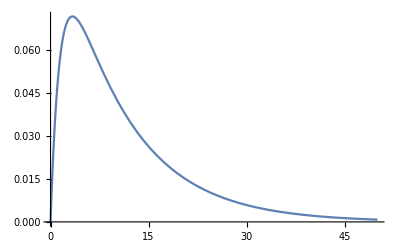

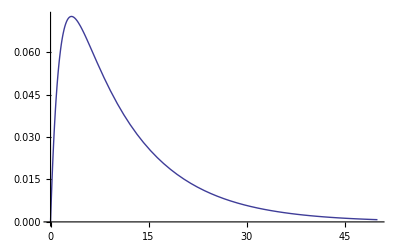

```mathematica
Plot[eps[t],{t,0,50}]
```

```mathematica
Integrate[eps[t],{t,0,∞}]
```

1.

### define stochastic intensity

```mathematica
(* escape noise for the dendrites *)
(*{ϕN,DϕN,DlϕN} = Block[ 
{k =100.(* firing at saturation *),β =5.0 (* Noise*),d =20000.0 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1+dd*Exp[-ββ*t]);
df =(kk*dd*ββ*Exp[-ββ*t])/(1+dd*Exp[-ββ*t])^2;
dlf = (ββ*dd)/(Exp[ββ*t]+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];*)
```

```mathematica
(* escape noise for the dendrites *)
{ϕN,DϕN,DlϕN} = Block[ 
{k =5.(* firing at saturation *),β =5.0 (* Noise*),d =1096.63 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1.0+dd*t);
df =(kk*dd*ββ*t)/(1.0+dd*t)^2;
dlf = (ββ*dd)/(1./t+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

```mathematica
(* escape noise for the soma *)
{ϕS,DϕS,DlϕS} = Block[ 
{k =k2,β =β2,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk ⅇ^(ββ *t);
df =kk ββ ⅇ^(ββ *t);
dlf = (*df/f*)ββ;
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

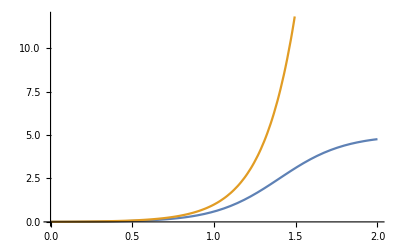

```mathematica
Plot[{ϕN[Exp[-β2 u]],ϕS[u]},{u,0,2}]
```

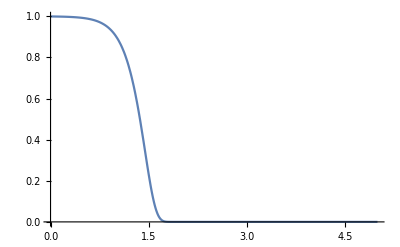

```mathematica
Plot[{step ϕS[u]/(ⅇ^(step ϕS[u])-1.)},{u,0,5},PlotRange->All]
```

```mathematica
step ϕS[u]/(ⅇ^(step ϕS[u])-1.)/.u->2
```

3.81504×10^-12

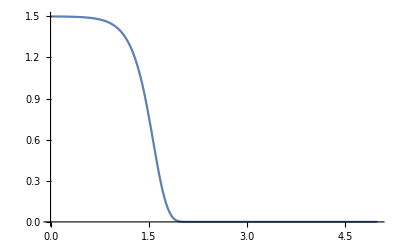

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]},{u,0,5},PlotRange->All]
```

```mathematica
1.-Exp[-ϕS[2.]step]
```

1.

```mathematica
Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]/.u->2.0
```

0.0013302

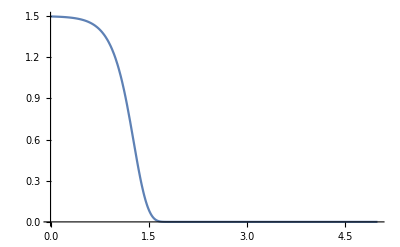

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]},{u,0,5},PlotRange->All]
```

```mathematica
Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]/.u->2.3
```

0.

### input: spikepattern X, corresponding synaptic potential epsps

```mathematica
Xin[]:=Block[{num=3,n,Xi},
    Xi:=(n=RandomInteger[PoissonDistribution[num]];
Sort[Table[RandomReal[] Tmax,{n}]]);
Table[Xi,{NN}]
];
```

```mathematica
Xin[]:=Block[{num=6,n,Xi},
    Xi:=(n=RandomInteger[PoissonDistribution[num]];
Select[Sort[Table[RandomReal[] 1000,{n}]],#≤Tonl&]);
Table[Xi,{NN}]
];
```

```mathematica
Inp[t_,X_,func_] :=
 (* add up the various spikes defined by <func> *)
Apply[Plus,
 func[
(* delete the negative times *)
 DeleteCases [t-X, a_/; a <0 ,{-1}]] ,
{1}(* only at the first level*) ];
```

```mathematica
Itimes = Table[ i step, {i,0,Floor[Tmax/step]}];
```

```mathematica
epsps[X_] :=Map[Inp[#,X,eps]&,Itimes]; (* Lists of synaptic potentials into each neuron for each (discretized) time *)
```

```mathematica
X = Xin[];
```

### define mempots

```mathematica
(* to calculate the membrane potential in the dendritic branchs *)
mempots[w_,inp_] := Block[ {tmp,us},
us=w.Transpose[inp]+Urest;
(*us= us* UnitStep[Umax-us]+Umax*UnitStep[us-Umax];*)(*saturation of the membrane potential at Umax *)
us
];
```

### define spikegenNMDA

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_]:=
Block[{usf=Flatten[us],spikesi,t},
(*spikesi=Sign[step * ϕN[usf]-RandomReal[{0,1},Length[usf]]];*)
spikesi=Sign[1.-Exp[-step * ϕN[usf]]-RandomReal[{0,1},Length[usf]]];
If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_,refPeriod_]:=
Block[{usf=Flatten[us],spikesi,t},
spikesi=Sign[step * ϕN[usf]*refPeriod-RandomReal[{0,1},Length[usf]]];If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

### define incrBuff

```mathematica
(* spike or not with escape noise *)
incrBuff[lindBuff_]:=
Block[{ind},
ind = Mod[lindBuff+1,stNMDA+1];
If[ind==0,1,ind]
];
```

### define myUnitStep

```mathematica
(Min[(tNMDA/(tNMDA+step)),Tonl/(Tonl+step)]+0.00001)/1000
```

0.000996026

```mathematica
myUnitStep[numb_]:=Block[{},
0.5*(Sign[(numb)+0.00099602593625498]+1.0)
];
```

### define ToFloat

```mathematica
ToFloat[numb_]:=Block[{numFl},
numFl=(numb*1.0);
numFl
];
```

### define SomaSat

```mathematica
SomaSat[u_]:=myUnitStep[UmaxSoma-u]u+myUnitStep[u-UmaxSoma]UmaxSoma;
```

### define stepper

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat,ToFloat},
{{myinps,_Real,2},   (* input potentials *)
{myOut,_Integer,1},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,nmyOut},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
nmyOut=myOut;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];

If[ToFloat@Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]]>0.5,Sow[ i];];

(* somatic spike *)
If[MemberQ[nmyOut,i],
EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
,

EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
Updinc =(step*DϕN[argFI]).thisinp;


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;

)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(τfrac*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(nτfracSp*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}(*,{MemberQ[_,_],_Boolean}*)}
];
```

```mathematica
GlobalRefs[stepper]
```

{}

### define passEpisode

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisode[w_, inps_, outps_] := passEpisode[inps,outps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisode[inps_,outps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepper[inps,outps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisode[inps_,outps_,lresl_] := (
passEpisode[inps,outps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisode[inps_,outps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisode[First@ww,inps,outps];
(* only if the second argument (ww_) is of type ini  *)
```

### define passEpisodeEval

```mathematica
stepperEval =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat},
{{myinps,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
nUspikeNMDA=UspikeNMDA;
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
nmyreset+=ntmrini;
Sow[ i];
];

(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeEval[w_, inps_] := passEpisodeEval[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeEval[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperEval[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeEval[inps_,lresl_] := (
passEpisodeEval[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeEval[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeEval[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define iniws (initial weights and Mask)

```mathematica
iniws[w_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Norm[w,1]/Length[w];tmp=Table[w,{num}]+RandomReal[NormalDistribution[0,tmp],{num,Length[w]}];Mask=RandomReal[{0,1},{num,Length[w]}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### define myiniws

```mathematica
myiniws[μw_,σw_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Table[μw,{num},{NN}];If[σw≠0,tmp+=RandomReal[NormalDistribution[0,σw],{num,NN}]];
Mask=RandomReal[{0,1},{num,NN}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### Def. functions to create patterns

```mathematica
Patn=5;
 
(* number of patterns *)
Pats=Table[Xin[],{Patn}];
```

```mathematica
FlucLen=0;
MakePats[]:=(Pats=Table[Xin[],{Patn}];PatLen=Table[1+Round[(Tonl+2 FlucLen (Tmax-Tonl) (RandomReal[]-0.5))/step],{Patn}];)
```

```mathematica
Patsepsps0[n_] := Take[epsps[Pats[[n]]],PatLen[[n]]];
Clear[Patsepsps]; 
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(* patters as potentials *)
```

```mathematica
(*InhibInp0[n_] :=Map[Total,RotateRight[Patsepsps[n],Round[τInhib/step]]];
Clear[InhibInp]; 
InhibInp[n_]:=InhibInp[n]=InhibInp0[n];*)
```

### define learn

```mathematica
rewdelay=0.;
learnEpisodes[wwin_,trials_,lstep_]:=Block[{last,ensrew=0,ww,n,c,o,nw,thisstep,dw,dwl,wl,cutoff,R,rewb,rews,resets,Z,Y,temp,t,punishCoeff,spTimings},
punishCoeff=Range[1,Round[Tonl/step]];
last=ini[wwin];
rewb=(R[#1,50+rewdelay,rewdelay,0.1]&)/@Itimes-1;
λ =0.2;
spTimings=Table[Round[i 500/(1+nbSp)/step],{i,nbSp}];
For[i=1,i≤trials,i++,
n=RandomInteger[{1,Patn}];
{last,{Y,Z}}=nextpassEpisode[Patsepsps[n],spTimings,last];
last=Last@last;(*we don't care about membrane pot*)

(*temp=o;*)
o=last[[4]]* Mask;

last[[1]]=last[[1]]+ lstep *(last[[4]]* Mask);(* weight update *)
temp=UnitStep[BoundSyn-Abs[last[[1]]]];
last[[1]]=temp*last[[1]]+(1.-temp)*BoundSyn;(* only weights smaller BoundSyn *)

ensrew=(1-λ) ensrew+λ (ensgood);(* performance percentage as running mean *)(*If[Mod[i-1,10]==0,msg[{i,n,t,ensfield,o,Length[Patsepsps[n]]}]];*)
Sow[{R,Z,Map[Length,Y],Max@Abs@o(*Norm[o]*),Norm@First@last},ensemble];
(*msg[Z];*)
];
First@last
];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

### define learnInFile

```mathematica
learnInFile[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,tmpSeed},
tmpSeed=IntegerPart[AbsoluteTime[]];
SeedRandom[tmpSeed];
Print["seed="<>ToString@tmpSeed];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(* patters as binarypotentials *)

tmp=Reap[learnEpisodes[wwin,trials1,lstep],ensemble];
res=trialDT[outDT[Transpose[tmp[[2,1]]][[1]](* Perf *)],
outDT[Transpose[tmp[[2,1]]][[2]](* Z *)],
outDT[Transpose[tmp[[2,1]]][[3]](* Y *)],
outDT[Transpose[tmp[[2,1]]][[4]](* |Δw| *)],
outDT[tmp[[1]](* w *)],
outDT[tmpSeed]];
PutAppend[res,(getFileName[lstep,trials1, opt])];

];
```

### define ContlearnInFile

```mathematica
ContlearnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,PerfTab,ZTab,YTab,ΔwTab,outFileName,outSeedtab},
outFileName=getFileName[lstep,trials1+trials2, opt];
res=ReadList[getFileName[lstep,trials1, opt]];

PerfTab=res/.trialDT[outDT[a_],_,_,_,_,_]->a;
ZTab=res/.trialDT[_,outDT[a_],_,_,_,_]->a;
YTab=res/.trialDT[_,_,outDT[a_],_,_,_]->a;
ΔwTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;


For[(*k=1,k≤Length@WTab,k++*)k=Length@WTab,1≤k,k--,
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];

outSeedtab=If[FileExistsQ[outFileName],ReadList[outFileName]/.trialDT[_,_,_,_,_,outDT[a_]]->a,{}];
If[FreeQ[outSeedtab,Seedtab[[k]]],
Print@Timing[tmp2=Reap[learnEpisodes[WTab[[k]],trials2,lstep,nbSp],ensemble];];
res=trialDT[outDT[Join[PerfTab[[k]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[ZTab[[k]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[Join[YTab[[k]],Transpose[tmp2[[2,1]]][[3]]](* Y *)],
outDT[Join[ΔwTab[[k]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[Seedtab[[k]]]
];
PutAppend[res,outFileName];
];
];
];
```

### λFilter

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_,iniV_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,iniV,incs]//Rest
];
```

## Plot functions

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

### Def PlotHistdFromFile

```mathematica
SigmaMaxStatTimings=50;
```

```mathematica
(* plot the output spike trains in a matrix*)
PlotHistdFromFile[nbTrials_,LearnRates_,opt_]:=
Block[{res,tmp,mm,sd,tmpStat,spTimings,PropFar,SigmaMaxStatTimings},
spTimings=Table[Round[i 500/(1+nbSp)],{i,nbSp}];
SigmaMaxStatTimings=Min@Abs[Differences[spTimings]]/2;
SigmaMaxStatTimings=20;
tmp=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
tmp=Map[Take[step*#,-50]& ,tmp];
tmpStat=Flatten@Map[#-spTimings&,tmp,{3}];
tmpStat=Select[tmpStat,Abs[#]<SigmaMaxStatTimings&];
PropFar=Length@tmpStat/Length@Flatten@tmp//N;
sd=StandardDeviation@Flatten@tmpStat;
mm=Mean@Flatten@tmpStat;
tmp=Flatten@Map[If[Length[#]==0,{0},#]&,tmp,{2}];
Histogram[tmp,(*Automatic*){2},"Probability",PlotRange->All,AxesLabel->{"t_s","P(t_s)"},
PlotLabel->Style[Framed["μ="<>ToString[mm]<>"σ="<>ToString[sd]<>";    P_in="<>ToString[PropFar]],16]]
];
```

### define PlotPerfInFile

```mathematica
PlotPerfInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_]->a;
ListLinePlot[ λFilter[1.5+Mean@res,0.2/Patn]-1.5,FrameLabel->{"trials","R(Z)"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{rewardFct[cSpikeTimeStep],0}]
];
```

```mathematica
PlotPerfsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_]->a;
ListAnimate@Table[ListLinePlot[ λFilter[res[[i]]+1.5,0.1/Patn]-1.5,FrameLabel->{"trials","R(Z)"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[i],
Frame->True,PlotRange->{rewardFct[cSpikeTimeStep],0}],{i,Length@res}]
];
```

```mathematica
PlotPerfInFile[names_,legends_]:=Block[{tmp,res},
res=Table[
λFilter[Mean[ReadList[n]/.trialDT[outDT[a_],_,_,_,_,_]->a]+1.5,0.1/Patn]-1.5,
{n,names}];
ListLinePlot[ res,FrameLabel->{"trials","R(Z)"},
PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True,PlotRange->{rewardFct[cSpikeTimeStep],0}]
];
```

### define PlotWeightsInFile

```mathematica
PlotWeightsInFile[trials_,lstep_,opt_]:=
Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,_,outDT[a_],_]->a;
res=Select[Flatten@res,(#≠0.0) &];
Histogram[res,Automatic(*{2}*),"Probability",PlotRange->All,AxesLabel->{"W","P(W)"},
PlotLabel->Style[Framed["μ="<>ToString[Mean@res]<>";    σ="<>ToString[StandardDeviation@res]],16]]
];
```

### define PlotWEvolInFile

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_]->a;

ListLinePlot[ λFilter[Mean@res,lambda],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotWEvolInFileList[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_]->a;
ListAnimate[Table[
ListLinePlot[ λFilter[res[[n]],1],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[n],
Frame->True,PlotRange->{0,1}]
,{n,1,Length@res}]]
];
```

### define PlotSigmaInFile

```mathematica
SigmaZero=0.;
```

```mathematica
ExtractStat[spTimes_]:=Block[{tmpStat,spTimings,tmp,SigmaMaxStatTimings},
If[Length@Flatten@spTimes<1,Return[{SigmaZero,0.}]];
spTimings=Table[Round[i 500/(1+nbSp)],{i,nbSp}];
SigmaMaxStatTimings=Min@Abs[Differences[spTimings]]/2;
SigmaMaxStatTimings=50;
tmpStat=Flatten@Map[#-spTimings&,spTimes,{2}];
tmpStat=Select[tmpStat,Abs[#]<SigmaMaxStatTimings&];
tmp=Length@tmpStat/Length@Flatten@spTimes//N;
{If[Length@tmpStat>1,StandardDeviation[tmpStat],SigmaZero],tmp}
];
```

```mathematica
PlotSigmaInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
(*tmp=Map[StandardDeviation@Flatten[
step If[Length@Flatten[#]>1,Flatten[#],{0,250}]
]&,Transpose@res];*)
tmp=Transpose@Map[ExtractStat[step #]&,Transpose@res];
{ListLinePlot[ λFilter[First@tmp,0.2/Patn,Mean@Take[First@tmp,3]],PlotRange->{0,20},FrameLabel->{"trials","σ"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True],
ListLinePlot[ λFilter[Last@tmp,0.2/Patn,Mean@Take[Last@tmp,3]],PlotRange->All,FrameLabel->{"trials","P_in"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True]}
];
```

```mathematica
PlotSigmaInFile[names_,legends_]:=Block[{tmp,res},
res=Transpose@Table[
tmp=ReadList[n]/.trialDT[_,outDT[a_],_,_,_,_]->a;
tmp=Transpose@Map[ExtractStat[step #]&,Transpose@tmp];
{λFilter[First@tmp,0.2/Patn,Mean@Take[First@tmp,3]],
λFilter[Last@tmp,0.2/Patn,Mean@Take[Last@tmp,3]]}
,{n,names}];
{ListLinePlot[ First@res,PlotRange->{0,20},FrameLabel->{"trials","σ"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True],
ListLinePlot[Last@res,PlotRange->All,FrameLabel->{"trials","P_in"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True]}
];
```

### define PlotMeanSomSpikeInFile

```mathematica
PlotMeanSomSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
res=Map[Length,res,{2}];
tmp=Mean@res;
{First@tmp,ListLinePlot[ λFilter[tmp,0.2/Patn,Mean@Take[tmp,2]],PlotRange->All,FrameLabel->{"trials","<|Z|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]}
];
```

### Def PlotSpikeActivity

```mathematica
(* plot the output spike trains in a matrix*)
PlotSpikeActivity[nbTrials_,LearnRates_,opt_]:=
Block[{tmp,resD,i,j,tmpLen,ReductFact=2},
resD=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
resD=Ceiling[resD step /ReductFact];

tmp=Table[0,{Length@First@resD},{Tonl/ReductFact+1}];
For[i=1,i≤1Length@resD,i++,
tmpLen=Length@(resD[[i]]);
For[j=1,j≤tmpLen,j++,
If[Length@resD[[i,j]]≠0,
tmp[[{tmpLen-j+1},resD[[i,j]]]]+=1;(*,
tmp[[{tmpLen-j+1},1]]+=1;*)];
];
];

MatrixPlot[tmp,DataRange->{{1,Tonl},{1,nbTrials}},AspectRatio->1,PlotLabel->"η="<>ToString[LearnRates]<>"  n="<>ToString[nbTrials],DataReversed->{True,False}]
];
```

```mathematica
(* plot the output spike trains in a matrix*)
PlotSpikeActivityPaper[nbTrials_,LearnRates_,opt_]:=
Block[{tmp,resD,i,j,tmpLen,ReductFact=2,ar=1.5},
resD=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
resD=Ceiling[resD step /ReductFact];

tmp=Table[0,{Length@First@resD+1},{Tonl/ReductFact+1}];
For[i=1,i≤1Length@resD,i++,
tmpLen=Length@(resD[[i]]);
For[j=1,j≤tmpLen,j++,
If[Length@resD[[i,j]]≠0,
tmp[[{tmpLen-j+1},(*1+Length@resD-*)resD[[i,j]]]]+=1;(*,
tmp[[{tmpLen-j+1},1]]+=1;*)];
];
];

MatrixPlot[Transpose@tmp,DataRange->{{1,nbTrials},{1,Tonl}},AspectRatio->1/GoldenRatio,DataReversed->{False,True},Axes->None,Frame->True,FrameTicks->{{0,Tonl/2,Tonl},{{0,nbTrials},nbTrials/2,{nbTrials,0}},None,None},BaseStyle->18,ImageSize->400]
];
```

### define PlotMeanBranchSpikeInFile

```mathematica
PlotMeanBranchSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_,_]->a;
res=Map[Length,res,{3}];
res=Map[Mean,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Y|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### define ToErrorList

```mathematica
ToErrorList[ls_,points_]:=Module[{mean,error},
mean=Prepend[Transpose[{Range[Min[Length/@ls]],(Mean@ls)[[Range[Min[Length/@ls]]]]}][[points]],{1,.5}];
error=Prepend[1/√(Length@ls)(StandardDeviation@ls)[[Range[Min[Length/@ls]]]][[points]],0];
MapThread[{#1,ErrorBar[#2]}&,{mean,error}]
]
```

## Changed Fct

### define getNbDSpikePerAPFromFile

```mathematica
GetNbNMDAForAP[Z_,Y_]:=Block[{tmp},
tmp=Map[Length@Cases[Map[Max,#-Y],x_/;(x>0&&x<stNMDA)] &,Z];
If[tmp=={},{},Mean@tmp]
]
```

```mathematica
getNbDSpikePerAPFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
N@Mean@Flatten@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
GetNbNMDAForAP[Z,Y]
,{k,Length@Seedtab}]
];
```

### define PlotMeanNMDAContrFromFile

```mathematica
PlotMeanNMDAContrFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
stepperlist=0;
Transpose[Most@Most@last][[3;;4]]
,{k,Length@Seedtab}];
res={Mean@First@res,Mean[res[[2]]],StandardDeviation[res[[2]]],{{250,0},{250,-UrestSoma}}};
ListLinePlot[ res,FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@First@res],"μ_AMPA="<>ToString[Mean[res[[2]]]],"σ_AMPA="<>ToString[Mean[res[[3]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]

];
```

### define GetFinalStatFromFile

```mathematica
myMean[data_]:=If[Length@data==0,{},Mean@data]
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{0},Z]}
]
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,Length@Seedtab}];
tmp=step*Cases[Flatten[res[[4]]],Except[0]];
{Mean[Flatten[res[[3]]]],
Histogram[Flatten[res[[4]]]*step,(*Automatic*){2},"Probability",
PlotLabel->Framed[Style["μ="<>ToString[Mean[tmp]]<>";    σ="<>ToString[StandardDeviation[tmp]],16]],PlotRange->All,AxesLabel->{"t_s","P(t_s)"}],
ListLinePlot[ {Mean[res[[1]]],Mean[res[[2]]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None],
ListAnimate[Table[
ListLinePlot[ {res[[1]][[k]],res[[2]][[k]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[k],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]
,{k,Length@First@res}],AnimationRunning->False]
}
];
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{0},Z]}
]
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,Length@Seedtab}];
tmp=step*Cases[Flatten[res[[4]]],Except[0]];
{Mean[Flatten[res[[3]]]],
Histogram[Flatten[res[[4]]]*step,(*Automatic*){2},"Probability",
PlotLabel->Framed[Style["μ="<>ToString[Mean[tmp]]<>";    σ="<>ToString[StandardDeviation[tmp]],16]],PlotRange->All,AxesLabel->{"t_s","P(t_s)"}],
ListLinePlot[ {Mean[res[[1]]],Mean[res[[2]]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None],
ListAnimate[Table[
ListLinePlot[ {res[[1]][[k]],res[[2]][[k]],{{250,0},{250,-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[k],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]
,{k,Length@First@res}],AnimationRunning->False]
}
];
```

## Simulations

```mathematica
NN=100;
UspikeNMDA=0.4;
nbNeuron=20;
pConnect=0.5;
Patn=1;
nbSp=3;
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
σW=4.1;(* c(Z)~52% and N(Z)~1.05 activity *)
```

### R-sdSP

```mathematica
η=4.5;
```

```mathematica
iter=10000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"],{20}];
```

seed=3657737124

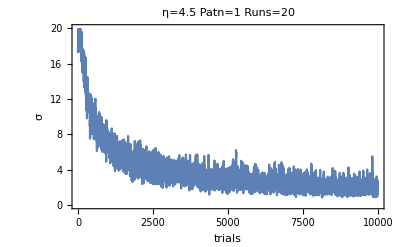
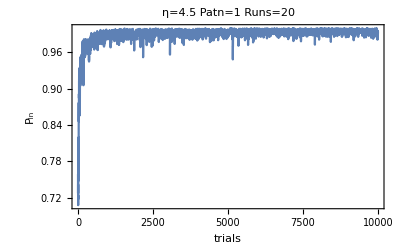

```mathematica
PlotSigmaInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

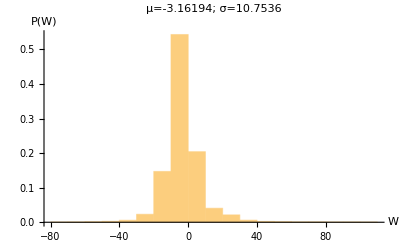

```mathematica
PlotWeightsInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

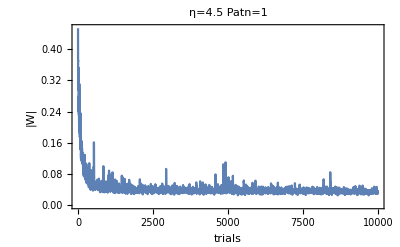

```mathematica
PlotWEvolInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin",0.2]
```

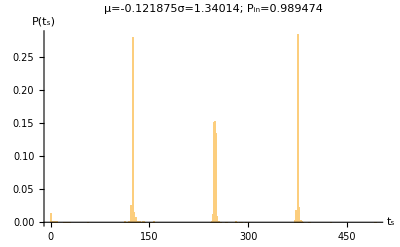

```mathematica
PlotHistdFromFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

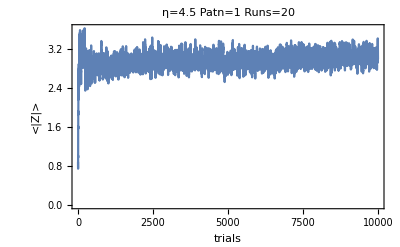
{23/20,-Graphics-}

```mathematica
PlotMeanSomSpikeInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

```mathematica
PlotSpikeActivity[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

-Graphics-

```mathematica
GetFinalStatFromFile[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

```mathematica
(* plot the output spike trains in a matrix*)
PlotSpikeActivityPaper[nbTrials_,LearnRates_,opt_]:=
Block[{tmp,resD,i,j,tmpLen,ReductFact=2},
resD=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
resD=Ceiling[resD step /ReductFact];

tmp=Table[0,{Length@First@resD+1},{Tonl/ReductFact+1}];
For[i=1,i≤1Length@resD,i++,
tmpLen=Length@(resD[[i]]);
For[j=1,j≤tmpLen,j++,
If[Length@resD[[i,j]]≠0,
tmp[[{tmpLen-j+1},(*1+Length@resD-*)resD[[i,j]]]]+=1;(*,
tmp[[{tmpLen-j+1},1]]+=1;*)];
];
];

MatrixPlot[Transpose@tmp,DataRange->{{1,nbTrials},{1,Tonl}},AspectRatio->0.35,DataReversed->{False,True},Axes->None,Frame->True,FrameTicks->{{0,Tonl/2,Tonl},None(*{{0,nbTrials},nbTrials/2,{nbTrials,0}}*),None,None},BaseStyle->20,ImageSize->400,FrameStyle->Directive[Thickness[0.01],Blue],FrameTicksStyle->Black,ImagePadding->{{37,25},{25,4}}]
];
```

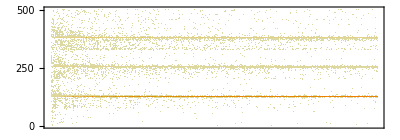

```mathematica
figPSTSpTimesSupervised=PlotSpikeActivityPaper[iter,η,"OnlineRuleAMPA_Supervised_Origin"]
```

```mathematica
Export["figSupervisedSpTimes.png",figPSTSpTimesSupervised,ImageResolution->600]
```

figSupervisedSpTimes.png

### R-sSP (R-sdSP but without the dendritic spike part)

#### core code

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat,ToFloat},
{{myinps,_Real,2},   (* input potentials *)
{myOut,_Integer,1},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,nmyOut},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
nmyOut=myOut;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];

If[ToFloat@Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]]>0.5,Sow[ i];];

(* somatic spike *)
If[MemberQ[nmyOut,i],
(*EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];*)
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
,

(*EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];*)
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc(*+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)*)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
(*Updinc =(step*DϕN[argFI]).thisinp;*)


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
(*us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;*)

)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(τfrac*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(nτfracSp*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}(*,{MemberQ[_,_],_Boolean}*)}
];
```

#### sumulations

```mathematica
η=0.266;
```

```mathematica
iter=5000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"],{15}];
```

seed=3580046607

$Aborted

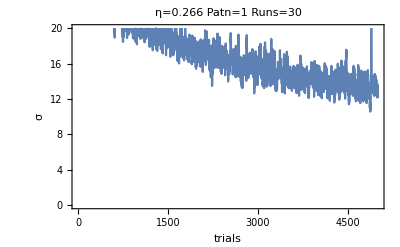
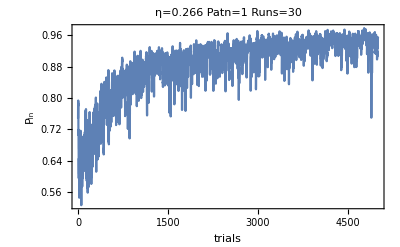

```mathematica
PlotSigmaInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

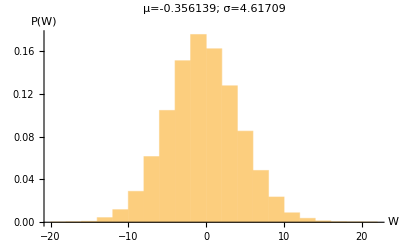

```mathematica
PlotWeightsInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

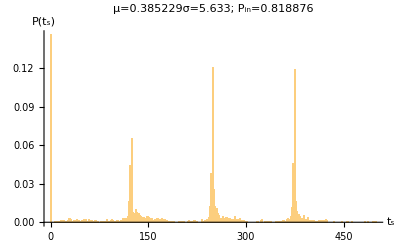

```mathematica
PlotHistdFromFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

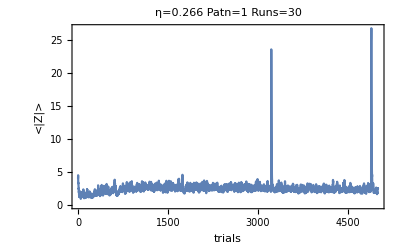
{71/30,-Graphics-}

```mathematica
PlotMeanSomSpikeInFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

```mathematica
PlotSpikeActivity[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

-Graphics-

```mathematica
GetFinalStatFromFile[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

```mathematica
(* plot the output spike trains in a matrix*)
PlotSpikeActivityPaper[nbTrials_,LearnRates_,opt_]:=
Block[{tmp,resD,i,j,tmpLen,ReductFact=2},
resD=ReadList[getFileName[LearnRates,nbTrials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
resD=Ceiling[resD step /ReductFact];

tmp=Table[0,{Length@First@resD+1},{Tonl/ReductFact+1}];
For[i=1,i≤1Length@resD,i++,
tmpLen=Length@(resD[[i]]);
For[j=1,j≤tmpLen,j++,
If[Length@resD[[i,j]]≠0,
tmp[[{tmpLen-j+1},(*1+Length@resD-*)resD[[i,j]]]]+=1;(*,
tmp[[{tmpLen-j+1},1]]+=1;*)];
];
];

MatrixPlot[Transpose@tmp,DataRange->{{1,nbTrials},{1,Tonl}},AspectRatio->0.35,DataReversed->{False,True},Axes->None,Frame->True,FrameTicks->{{0,Tonl/2,Tonl},{{0,nbTrials},nbTrials/2,{nbTrials,0}},None,None},BaseStyle->20,ImageSize->400,FrameStyle->Directive[Thickness[0.01],Magenta],FrameTicksStyle->Black,ImagePadding->{{37,25},{25,4}}]
];
```

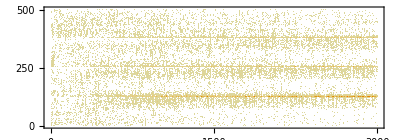

```mathematica
figPSTSpTimesPfisterSupervised=PlotSpikeActivityPaper[iter,η,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

```mathematica
Export["figSupervisedSpTimesPfister.png",figPSTSpTimesPfisterSupervised,ImageResolution->600]
```

figSupervisedSpTimesPfister.png

### Plot stats

```mathematica
PosEmpSptTrain=570.;
```

```mathematica
GetFinalStatData[fileName_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20},
res=ReadList[fileName];
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{},Z]}
]
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,Length@Seedtab}];
tmp=step*Cases[Flatten[res[[4]]],Except[0]];
{Flatten[res[[3]]],
Flatten[res[[4]]]*step,
res[[1]],res[[2]]
}
];
```

```mathematica
FileNamePST=getFileName[η,5000,"OnlineRuleAMPA_Supervised_Origin"]
```

./out/_eta4.5_trials5000_IL100_NbNeurons20_USpike0.4_Patn1_SigmaW4.1_NbSp3_aAMPA0.0632455_OnlineRuleAMPA_Supervised_Origin.out

```mathematica
{mNbdSpForAP,spTimes,NMDAinp,AMPAinp}=GetFinalStatData[FileNamePST];
```

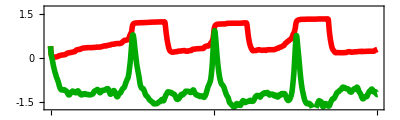

```mathematica
PlotMeanAct=ListLinePlot[{ Mean@Map[λFilter[#,0.2]&,NMDAinp],Mean@Map[λFilter[#,0.2]&,AMPAinp] (*,Mean@Map[λFilter[#,0.2]&,NMDAinpNoAMPA] ,Mean@Map[λFilter[#,0.2]&,AMPAinpNoNMDA]*)},Joined->True,Frame->True,Axes->False,ImageSize->400,BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,500},PlotRange->{-1.7,1.7},PlotStyle->{{Red,Thickness[0.01]},{Darker@Green,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Darker@Green,Dashed,Thickness[0.01]}},FrameTicks->{ {0,250,500},{ -1.5,0,1.5}, None, None},AspectRatio->0.3,ImagePadding->{{39,30},{27,0}}]
```

```mathematica
Export["PlotMeanAct_supervised.png",PlotMeanAct]
```

PlotMeanAct_supervised.png

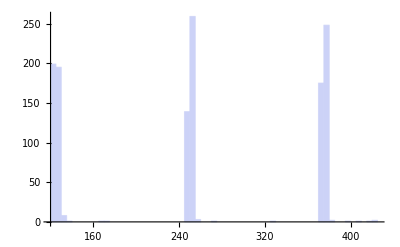

```mathematica
Histogram[spTimes,{5}]
```

```mathematica
Mean[spTimes]
```

252.917

```mathematica
Mean[Select[spTimes,#<(PosEmpSptTrain-1)&]]
```

252.917

```mathematica
StandardDeviation[Select[spTimes,#<(PosEmpSptTrain-1)&]]
```

102.85

```mathematica
η=0.266;
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
UspikeNMDA=0.4;
σW=4.1;(* c(Z)~52% and N(Z)~1.05 activity *)
FileNamePfisterPST=getFileName[η,5000,"OnlineRuleAMPA_Supervised_Origin_OnlyPfister"]
```

./out/_eta0.266_trials5000_IL100_NbNeurons20_USpike0.4_Patn1_SigmaW4.1_NbSp3_aAMPA0.0632455_OnlineRuleAMPA_Supervised_Origin_OnlyPfister.out

```mathematica
{mNbdSpForAPPfister,spTimesPfister,NMDAinpPfister,AMPAinpPfister}=GetFinalStatData[FileNamePfisterPST];
```

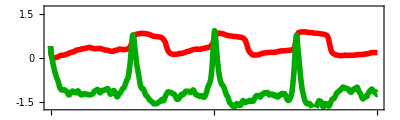

```mathematica
NMDAinpPfister=ListLinePlot[{ Mean@Map[λFilter[#,0.2]&,NMDAinpPfister],Mean@Map[λFilter[#,0.2]&,AMPAinp] (*,Mean@Map[λFilter[#,0.2]&,NMDAinpNoAMPA] ,Mean@Map[λFilter[#,0.2]&,AMPAinpNoNMDA]*)},Joined->True,Frame->True,Axes->False,ImageSize->400,BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,500},PlotRange->{-1.7,1.7},PlotStyle->{{Red,Thickness[0.01]},{Darker@Green,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Darker@Green,Dashed,Thickness[0.01]}},FrameTicks->{ {0,250,500},{ -1.5,0,1.5}, None, None},AspectRatio->0.3,ImagePadding->{{39,30},{27,0}}]
```

```mathematica
Export["PlotMeanActPfister_supervised.png",NMDAinpPfister]
```

PlotMeanActPfister_supervised.png

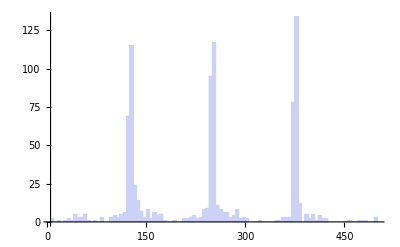

```mathematica
Histogram[spTimesPfister,{5}]
```

```mathematica
Mean[Select[spTimesPfister,#<(PosEmpSptTrain-1)&]]
```

244.981

```mathematica
StandardDeviation[Select[spTimesPfister,#<(PosEmpSptTrain-1)&]]
```

106.544

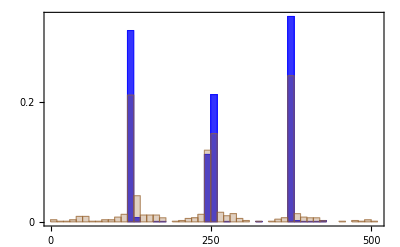

```mathematica
PlotSpTime=Histogram[{spTimes,spTimesPfister~Join~{0,500}},{10},"Probability",(*FrameLabel->{"Perf (%)","P(Perf)"},*)BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),ChartStyle->{Directive[Blue,Opacity[0.8]],Directive[Brown,EdgeForm[Dashed],Opacity[0.3]]},Axes->False,ImageSize->400,Frame->{{False,False},{True,False}},FrameTicks->{{{0,0.2,0.4},None},{{{0,0},{250,250},{500,500},{PosEmpSptTrain,"∅"}},None}},ImageSize->400,PlotRange->All,PlotRangePadding->{{0,10},{0.,0.01}}]
```

```mathematica
rip[graphics_, {xl_, xh_}, {yl_, yh_}] := Block[ {t, is, pr},
  t = ImportString[ExportString[graphics, "EPS"], "EPS"];
  is = ImageSize /. Cases[t, HoldPattern[ImageSize -> _], Infinity];
  pr = is {{xl, xh}, {yl, yh}};
  is = is {xh - xl, yh - yl};
  t /. (PlotRange -> _) -> (PlotRange -> 
       pr) /. (ImageSize -> _) -> (ImageSize -> is) 
  ]
```

```mathematica
Export["PlotSpTimeR-supervis.png",PlotSpTime]
```

PlotSpTimeR-supervis.png

```mathematica
{spTimes,spTimesPfister~Join~{0}}
```

{{123.,249.6,375.2,375.4,126.6,375.2,125.,250.,375.6,124.8,248.4,372.8,125.,250.4,375.8,125.2,248.8,371.8,376.2,125.4,250.6,374.2,124.8,251.,376.6,125.6,253.2,375.4,125.2,251.2,375.4,251.,375.8,125.4,252.,370.8,124.,248.,252.6,375.8,376.4,125.6,251.2,375.2,125.,251.6,375.6,125.4,250.4,375.8,124.8,375.8,125.,251.6,375.4,124.6,250.8,375.,125.,251.4,376.,125.2,250.,251.8,374.6,124.2,250.,374.8,125.2,250.2,375.,125.2,249.8,376.,124.,250.,250.2,375.,125.8,250.2,374.8,126.6,250.,375.,124.6,250.,374.8,124.4,249.6,251.8,374.4,125.4,250.,374.8,125.8,250.,250.4,374.8,124.6,250.,374.6,125.8,250.,375.,124.6,250.4,375.6,124.,249.8,374.6,124.6,250.4,375.,126.4,250.,375.,125.8,127.4,250.,375.,125.2,250.4,374.8,125.,250.,375.8,127.,128.,249.8,375.2,124.8,248.4,374.4,123.8,248.6,250.8,374.8,124.4,250.8,125.6,127.6,248.4,375.8,126.,250.6,374.4,126.,248.2,250.6,374.,126.,250.4,374.8,125.,129.8,250.,375.6,125.6,250.,375.8,124.2,249.6,374.6,124.4,250.6,251.8,376.,125.6,249.2,376.2,124.2,250.4,375.2,124.2,248.,375.2,124.6,250.,375.,377.4,124.6,249.8,375.2,125.8,250.2,374.8,124.4,248.8,374.8,125.4,250.4,374.4,124.2,251.,374.4,125.4,249.8,375.,124.4,250.2,374.8,124.8,374.8,124.2,250.4,374.6,123.8,250.2,375.2,250.4,375.2,406.8,123.,250.2,375.6,125.2,250.4,374.8,124.2,250.6,375.2,124.2,249.6,375.,124.6,250.,375.2,124.,250.2,375.2,124.4,249.2,374.8,124.8,250.2,374.8,124.8,250.2,375.,125.6,250.2,374.6,125.4,249.2,375.4,124.2,250.8,375.,125.,251.,375.2,123.,250.,374.8,123.,251.,254.4,375.,121.4,250.6,254.6,375.,123.4,247.,255.4,375.,124.6,249.8,375.4,250.4,375.2,123.6,250.6,255.,375.4,399.6,250.,374.8,251.2,375.2,122.,250.2,375.2,121.6,251.,375.,121.6,130.6,251.,374.6,122.,135.8,250.2,374.6,250.,375.,121.,251.,375.4,377.,251.6,253.4,375.,125.6,250.6,374.8,128.4,250.,375.2,124.2,250.,374.4,249.6,374.4,122.2,250.,375.,124.8,249.8,375.4,132.8,250.8,271.8,373.8,123.6,249.,374.2,126.,249.,375.4,124.6,249.8,374.4,123.4,249.8,374.8,125.8,249.8,375.,124.6,250.2,374.8,125.,249.8,375.,125.,249.6,375.,380.,130.6,250.6,374.6,127.6,250.8,374.8,377.,123.4,249.8,375.,124.2,249.,374.8,379.,124.,250.8,374.8,378.,124.8,249.8,374.8,124.2,132.4,250.2,375.6,125.2,250.6,375.6,128.8,250.4,374.8,124.4,250.,375.4,126.2,250.6,375.,124.8,247.8,374.8,123.4,249.4,374.8,378.4,124.2,128.2,249.6,373.4,126.8,375.2,124.4,129.2,248.2,372.8,126.,250.,375.,124.6,249.6,374.8,126.6,249.8,374.8,126.6,251.2,374.6,125.,127.8,375.2,125.2,172.4,249.8,375.2,124.,125.6,374.2,125.8,129.,374.8,127.4,251.4,375.2,126.6,249.4,375.2,125.,375.,375.4,124.8,250.8,375.,124.8,251.8,374.8,124.8,250.,372.8,378.6,124.8,250.2,376.6,124.8,250.8,375.,124.6,248.2,376.2,125.,249.8,376.,125.,249.6,370.4,377.8,124.6,249.8,376.4,124.6,250.,374.2,250.,376.6,124.6,249.8,376.8,249.2,373.8,124.4,250.2,376.2,124.2,250.,377.,123.6,249.2,370.8,125.,250.2,378.2,124.6,250.2,250.4,375.2,124.6,249.8,372.,378.8,124.4,249.8,379.4,125.2,250.8,377.,124.8,249.8,370.8,124.6,251.,372.8,125.,250.2,372.,377.,124.,251.,125.,249.2,375.8,124.6,249.6,373.4,124.2,249.6,125.,249.6,371.8,125.4,375.8,124.2,250.2,371.4,124.4,249.6,375.6,124.4,250.2,376.6,125.6,124.8,249.8,124.8,125.6,374.4,125.2,375.,126.4,251.2,126.2,250.,373.8,124.8,372.4,124.6,329.6,250.,372.8,123.6,249.6,375.8,122.8,249.8,376.2,127.6,248.6,376.2,250.2,375.,124.8,375.6,123.6,250.,375.2,123.2,250.2,375.,126.8,249.8,372.6,372.8,380.8,249.6,373.4,379.8,250.,372.2,249.6,375.,123.2,249.2,250.6,371.6,123.,126.6,249.2,251.,374.2,122.8,249.8,375.8,123.4,250.8,372.8,122.2,250.2,372.8,376.4,123.8,249.8,375.4,124.8,250.2,379.2,124.8,249.8,374.6,125.,250.,377.,124.8,249.8,374.4,377.4,125.2,249.8,376.4,124.6,250.6,372.6,376.2,125.4,250.,373.8,125.2,249.4,375.,125.2,250.,375.2,124.8,250.,374.6,124.8,250.,374.4,124.8,126.,249.8,375.6,125.2,250.,373.,125.2,250.2,374.8,125.2,249.8,375.6,124.8,126.,250.2,374.8,124.2,250.4,376.,125.2,250.,375.,125.,250.,375.,125.2,250.2,374.8,125.,250.,374.8,124.8,249.4,374.8,124.2,250.2,373.8,124.8,249.6,374.8,125.2,249.8,374.8,249.8,375.2,376.,125.,250.,374.8,125.,249.8,373.8,124.6,250.4,374.6,124.6,249.6,374.,124.8,250.2,375.2,376.4,125.,250.2,375.6,125.,250.,375.,124.6,250.4,375.2,124.2,250.2,375.4,376.6,124.4,250.2,375.,123.8,251.,376.,125.,249.4,374.4,125.,250.6,374.6,124.8,250.,375.,125.4,250.2,375.4,125.2,125.8,248.8,250.6,375.2,377.,125.2,251.6,374.,125.4,250.4,375.2,124.2,250.6,376.4,123.,250.8,374.6,375.6,123.4,250.2,374.2,124.8,249.6,377.,378.4,125.,126.4,250.8,374.8,124.8,249.2,375.,125.2,249.6,375.2,125.4,249.8,375.2,122.4,249.2,374.4,125.4,249.2,375.2,125.2,248.8,253.,375.4,124.4,128.2,250.,374.2,124.8,250.6,374.4,121.6,249.6,375.8,419.2,128.4,249.6,253.6,374.,123.8,127.4,250.2,375.,126.2,249.8,374.8,121.4,250.8,375.2,125.,250.,375.4,123.4,250.,374.6,122.4,249.8,374.6,375.8,121.6,168.8,250.,251.8,375.,126.4,250.4,252.8,375.,127.4,250.4,375.,126.4,250.,374.8,127.4,249.4,375.,121.8,249.8,374.8,126.2,249.6,374.6,121.,252.,375.,123.8,250.,375.,376.4,125.8,250.6,375.,376.4,125.6,375.,251.,375.,124.,251.4,374.8,376.2,126.,250.4,375.4,124.6,250.,375.2,126.6,252.4,374.8,124.8,250.2,375.4,124.8,250.,373.8,125.2,249.8,374.,125.2,250.2,374.,376.4,125.,250.2,373.4,124.8,250.,376.,125.2,126.,250.,374.6,125.,250.,374.4,125.2,249.8,374.,125.,125.8,250.2,373.4,124.8,249.8,375.,124.6,250.2,125.4,250.2,374.2,125.6,249.8,375.8,376.6,125.,250.2,376.8,125.,250.6,374.8,124.8,250.,373.2,124.6,250.,374.2,420.8,125.,250.4,377.2,124.8,249.8,250.4,377.6,249.6,374.8,122.2,249.8,375.,251.2,375.2,125.,249.8,255.6,374.6,124.8,249.8,374.6,123.6,250.4,374.4,123.8,248.6,254.8,374.6,120.8,252.,375.4,127.4,250.,252.,375.,249.2,374.6,121.6,250.4,374.8,121.4,250.,374.6,122.8,250.,375.4,126.6,249.,375.2,123.2,249.4,374.4,123.8,250.8,374.8,124.6,249.,374.6,122.4,250.2,374.,121.,249.8,375.2,250.,124.4,250.2,374.4,124.6,249.8,374.6,125.6,250.,374.2,124.6,250.2,124.6,250.4,253.,375.8,125.4,250.2,374.2,125.6,250.2,374.6,125.2,250.2,374.6,125.,250.4,375.6,124.6,250.,252.4,124.6,250.,374.6,125.6,126.2,249.8,374.6,125.2,250.4,374.8,124.8,249.8,374.2,125.,250.4,373.8,125.2,249.6,375.4,125.,249.8,374.8,125.,125.8,250.2,375.,125.,250.,374.,124.8,249.6,374.6,121.,250.4,375.2,123.,250.,252.8,375.2,122.2,250.2,376.,126.,250.4,375.2,123.2,249.6,373.8,126.2,250.6,374.,127.2,250.4,374.6,123.8,130.8,248.8,376.2,122.,249.6,375.8,125.6,250.2,374.8,126.6,250.,375.,125.2,250.2,374.4,122.,250.4,375.,126.4,250.,375.6,124.8,249.6,375.,122.6,250.,375.4,122.4,250.2,375.6,125.4,249.4,374.8,127.8,250.2,375.4,125.4,250.,375.4,124.8,374.8,375.8,125.,247.6,375.,124.6,131.,374.6,125.6,133.6,245.8,375.2,375.,420.6,125.2,375.,125.8,247.6,375.2,126.6,375.,131.8,246.4,375.2,126.2,246.6,375.,125.6,247.,374.6,125.2,375.2,123.8,129.,373.8,127.2,246.8,374.8,128.2,375.4,125.8,249.8,375.,125.,247.2,374.8,375.4,124.4,375.,124.8,252.,375.4,375.8,124.4,375.2,376.,124.8,249.4,374.8,124.6,250.,375.6,124.8,249.6,250.6,375.2,125.2,249.4,375.2,124.6,250.,374.8,125.,250.,376.2,125.,250.,375.,124.6,249.8,374.8,124.8,250.4,375.,125.,250.4,375.,375.2,250.2,373.6,124.2,249.4,375.,126.6,250.,375.,125.2,250.,375.4,124.6,250.2,375.2,125.,250.2,375.,125.4,249.6,375.,125.8,250.,375.,124.6,249.8,375.,125.,250.,374.8},{250.2,265.,127.6,375.4,250.4,126.8,124.8,127.6,128.4,251.8,373.4,264.4,288.4,125.,125.2,127.4,499.2,248.4,376.4,250.,123.8,124.4,374.4,498.,250.,479.6,497.6,127.4,131.4,250.,374.6,390.6,126.4,124.8,251.2,125.4,136.4,151.8,125.6,140.6,165.,250.4,125.,126.6,370.6,251.,126.2,248.6,252.2,251.,268.4,376.2,15.8,246.6,123.8,126.2,253.,377.4,125.4,377.8,124.6,255.6,374.2,250.6,125.6,124.6,254.,375.2,124.,242.8,252.,123.4,127.4,141.,161.,252.,279.4,250.,121.4,274.8,374.8,128.8,378.2,124.4,149.2,375.2,124.8,129.,376.4,122.6,246.4,254.8,383.6,125.,121.6,124.2,246.8,250.6,284.4,125.,374.4,128.,378.8,249.8,376.2,125.,245.,122.,374.2,128.4,247.8,251.8,285.,124.,375.4,251.8,374.6,375.6,124.8,374.6,376.6,401.4,137.,248.6,250.2,269.,281.2,287.8,122.8,250.8,237.2,249.8,251.4,287.8,376.2,124.4,252.8,376.4,122.8,245.2,252.2,264.2,287.4,376.6,46.8,128.2,160.,374.6,163.6,248.6,38.,123.4,138.8,165.8,248.,373.6,103.6,126.,134.,376.,123.8,377.2,80.6,253.,48.6,247.4,128.4,374.4,126.2,373.4,416.8,245.2,380.,391.8,381.,243.2,261.8,135.4,248.6,128.6,374.2,153.6,380.2,40.2,136.4,248.2,251.6,127.,248.,125.6,125.,374.8,224.6,248.,126.2,125.,248.8,376.2,123.6,248.8,252.2,376.,250.2,123.2,128.2,148.4,224.4,253.4,250.2,125.8,374.6,480.8,121.6,252.6,251.,123.6,376.6,40.4,127.,359.,250.4,375.,127.2,234.,374.,377.4,32.4,377.,43.2,54.,248.8,378.8,231.2,127.8,141.,159.4,173.,249.4,379.8,251.8,375.4,126.6,244.8,251.2,127.4,169.6,375.2,246.8,27.6,127.,248.2,249.8,252.4,376.,31.8,124.2,129.6,248.6,376.2,127.4,251.8,126.4,321.,375.8,131.4,216.4,129.2,376.2,121.6,132.6,125.4,238.8,364.6,128.2,134.6,131.4,213.4,241.2,126.,245.2,123.6,128.6,250.2,373.,372.,416.6,126.2,377.6,126.6,140.6,163.6,373.6,126.2,128.8,123.4,247.8,127.4,130.2,117.2,129.4,250.2,125.2,127.2,249.2,9.4,48.4,253.4,122.6,255.2,297.6,378.,249.6,376.6,370.6,9.6,248.6,103.6,113.,122.2,125.,129.6,250.6,373.2,123.2,299.,375.8,172.,374.8,133.,250.8,373.6,375.2,401.6,248.6,252.8,376.,132.4,374.,132.6,375.6,413.6,130.4,219.2,240.8,250.2,130.,247.8,380.8,129.8,250.2,375.2,410.6,131.2,250.2,376.4,130.,374.8,377.6,381.8,249.2,374.,376.4,129.2,129.4,240.2,257.,374.8,120.2,375.4,133.,252.8,375.2,239.6,247.2,353.4,379.2,128.8,383.,376.2,250.,376.8,248.6,161.8,251.6,295.2,372.8,250.,120.2,153.,248.6,378.4,372.,374.4,255.6,378.,171.8,250.8,250.8,374.8,139.,248.4,376.,127.4,372.4,50.6,249.2,381.2,377.6,123.4,249.4,246.8,378.4,119.8,254.6,249.4,379.6,252.2,119.6,126.2,250.2,261.2,268.4,293.4,255.8,217.2,232.4,249.4,373.8,124.6,125.6,143.6,192.8,213.6,376.4,124.6,248.8,124.6,136.,250.2,124.,125.6,252.,375.,126.,376.2,139.8,250.,270.,375.4,126.2,251.8,356.4,373.,378.8,131.2,375.4,402.,127.4,108.6,127.4,154.,174.8,249.4,125.,130.,58.6,125.,95.4,123.6,130.8,163.6,375.,128.4,346.,127.4,151.8,246.8,58.8,105.,220.2,255.,127.6,253.,54.6,100.6,124.8,372.,55.6,72.8,99.6,122.4,128.,246.4,125.6,135.2,236.,253.,122.8,361.8,125.,58.6,95.4,121.2,126.2,122.2,126.2,281.8,56.8,124.,128.,172.,249.4,359.8,368.6,384.,373.2,127.4,136.8,120.8,376.,376.2,122.8,374.4,112.8,137.4,375.6,252.2,375.8,375.4,137.4,245.2,249.4,375.2,121.2,133.8,154.,373.6,247.4,376.6,250.,376.4,135.6,126.4,378.6,247.4,375.4,246.4,376.4,374.8,124.4,247.2,377.6,249.,252.6,376.4,127.8,146.8,116.,128.2,141.4,377.,412.2,128.2,109.,246.8,124.6,252.8,272.,374.,250.8,252.,270.,374.8,378.6,391.8,124.8,251.,408.2,251.2,377.,102.6,116.,128.4,249.,127.2,250.,247.4,253.,374.8,248.8,253.2,374.2,127.8,250.4,256.8,374.6,247.8,250.6,125.8,129.6,373.8,125.6,245.8,121.,245.8,251.4,123.4,130.,133.4,249.8,374.,250.6,378.6,238.6,248.6,378.,248.4,286.4,379.,166.8,245.4,374.2,40.2,248.6,375.2,377.2,249.4,375.,253.4,376.,378.4,125.6,376.8,122.2,128.2,246.,370.6,124.4,246.2,375.4,376.8,424.8,123.2,249.8,374.4,250.2,260.2,251.6,251.2,374.4,377.4,134.4,248.8,373.2,119.8,151.6,377.6,375.,251.6,63.4,251.4,377.4,374.6,375.8,175.,248.6,374.6,371.2,379.,250.2,114.8,258.8,290.2,373.4,239.,374.4,112.8,373.,375.8,246.,262.,270.4,285.,375.6,376.6,375.4,248.,374.4,375.2,375.8,249.,124.4,251.2,127.8,250.2,125.8,249.8,260.6,129.6,252.8,125.,126.,140.6,127.,133.8,249.8,127.2,249.6,125.6,250.2,250.2,125.4,127.2,252.8,127.2,250.6,128.,250.2,250.6,376.8,251.,251.,250.2,250.,250.6,375.6,382.8,360.6,372.8,253.4,249.6,373.2,378.6,242.6,250.6,266.2,249.2,368.2,375.2,376.2,391.4,411.2,249.2,371.4,376.2,374.6,379.,250.4,378.2,390.2,125.2,158.4,250.6,249.4,252.,249.8,249.8,375.2,124.2,371.8,375.6,381.2,241.8,250.4,254.4,276.,375.,397.2,250.2,377.8,404.2,121.2,375.4,473.,126.2,263.8,375.2,121.2,206.4,252.6,376.6,127.6,374.6,376.6,122.6,255.8,374.4,249.6,376.,246.4,273.,374.2,377.8,250.4,373.,377.8,456.,122.8,134.4,250.4,302.8,125.,252.,373.8,377.6,246.,253.8,377.8,208.4,236.2,247.2,250.,256.2,277.8,41.6,124.8,253.2,377.2,126.8,266.4,283.,300.2,376.6,424.2,373.8,236.,250.6,375.4,121.4,372.6,376.8,251.2,376.2,243.8,373.8,153.6,374.2,247.8,375.8,81.6,111.6,374.6,375.8,248.8,123.8,248.8,289.2,374.8,247.4,253.,125.8,366.8,375.2,377.2,397.2,228.4,259.8,377.,138.4,375.,220.,122.2,249.4,377.6,228.8,82.,374.,374.8,380.,402.8,0}}

```mathematica
interCount=N@Range[0,500,10];
```

```mathematica
HistSpTimes=BinCounts[spTimes,{interCount}]/Length@spTimes;
```

```mathematica
θp=0.02500000000000000000000000000000001;
```

```mathematica
SelectHistSpTimes=UnitStep[HistSpTimes-θp]* θp+HistSpTimes UnitStep[θp-HistSpTimes];
```

```mathematica
SelectHistSpTimes2=UnitStep[HistSpTimes-θp]* HistSpTimes;
```

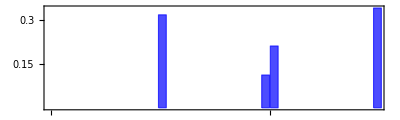

```mathematica
bChart11=BarChart[SelectHistSpTimes2,ChartStyle->Table[Directive[Blue,Opacity[0.7]],{Length@interCount}],(*ChartLabels->AxeLabel,*)BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),Axes->False,Frame->{{True,False},{False,False}},FrameTicks->{{{0.3,0.15},None},{{0,{Length@interCount/2,250},{Length@interCount,500}},None}},ImageSize->400,PlotRangePadding->{{0,15},{0,0.003}},AspectRatio->0.3,PlotRange->{{0,Length@interCount-13},All},ImagePadding->{{50,5},{0,0}}]
```

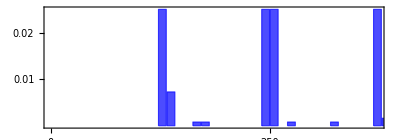

```mathematica
bChart1=BarChart[SelectHistSpTimes,ChartStyle->Table[Directive[Blue,Opacity[0.7]],{Length@interCount}],(*ChartLabels->AxeLabel,*)BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{{0.01,0.02},None},{{0,{Length@interCount/2,250},{Length@interCount,500}},None}},ImageSize->400,PlotRangePadding->{{0,15},{0.,0.003}},AspectRatio->0.35,PlotRange->{{0,Length@interCount-13},All},ImagePadding->{{50,5},{25,0}}]
```

```mathematica
HistSpTimesPfister=BinCounts[spTimesPfister,{interCount}]/Length@spTimesPfister;
```

```mathematica
SelectHistSpTimesPfister=UnitStep[HistSpTimesPfister-θp]* θp+HistSpTimesPfister UnitStep[θp-HistSpTimesPfister];
```

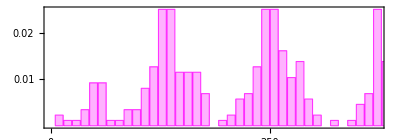

```mathematica
bChart2=BarChart[SelectHistSpTimesPfister,ChartStyle->Table[Directive[Magenta,Opacity[0.3]],{Length@interCount}],(*ChartLabels->AxeLabel,*)BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{{0.01,0.02},None},{{0,{Length@interCount/2,250},{Length@interCount,500}},None}},ImageSize->400,PlotRangePadding->{{0,15},{0.,0.003}},AspectRatio->0.35,PlotRange->{{0,Length@interCount-13},All},ImagePadding->{{50,5},{25,0}}]
```

```mathematica
SelectHistSpTimesPfister2=UnitStep[HistSpTimesPfister-θp]* HistSpTimesPfister;
```

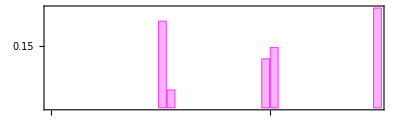

```mathematica
bChart22=BarChart[SelectHistSpTimesPfister2,ChartStyle->Table[Directive[Magenta,Opacity[0.3]],{Length@interCount}],(*ChartLabels->AxeLabel,*)BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),Axes->False,Frame->{{True,False},{False,False}},FrameTicks->{{{0.3,0.15},None},{{0,{Length@interCount/2,250},{Length@interCount,500}},None}},ImageSize->400,AspectRatio->0.3,PlotRangePadding->{{0,12},{0,0.003}},PlotRange->{{0,Length@interCount-13},All},ImagePadding->{{50,5},{0,0}}]
```

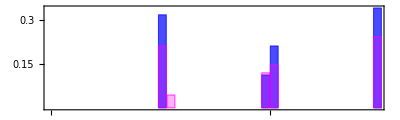

```mathematica
PlotSpTimeUp=Show[bChart11,bChart22,ImagePadding->{{50,5},{0,0}}]
```

```mathematica
Export["PlotSpTimeSupervised-Up.png",PlotSpTimeUp]
```

PlotSpTimeSupervised-Up.png

```mathematica
Export["PlotSpTimeSupervised-Up.png",-Graphics-,ImageResolution->600]
```

PlotSpTimeSupervised-Up.png

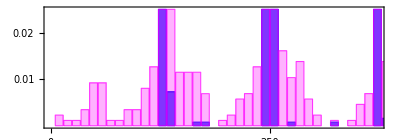

```mathematica
PlotSpTimeDown=Show[bChart1,bChart2,ImagePadding->{{50,5},{25,0}}]
```

```mathematica
Export["PlotSpTimeSupervised-Down.png",PlotSpTimeDown]
```

PlotSpTimeSupervised-Down.png

```mathematica
Export["PlotSpTimeSupervised-Down.png",-Graphics-,ImageResolution->600]
```

PlotSpTimeSupervised-Down.png